## Legend for coloring

Flow of the discussion and labels for the action being performed.

Technical comments (mostly on the Mathematica commands).

Comments and thoughts on what we are seeing.

## Technical Setup

Define some system-specific variables here - e.g. the base path for where the data files are stored. For some reason, Mathematica does not import the file successfully if it’s just located in the same folder and the path is omitted.

```mathematica
pathBase="/Users/ivanevtimov/GDrive-Laf/THESIS/Results with more subjects/";
```

```mathematica
fullData=Import["vgg_output_one_img_per_type_per_subject.csv",Path->pathBase,HeaderLines->1];
```

Define function functions for accessing the data. Note that these functions (or most of them) do not work over the index but over the row itself provided as an argument. That is because functions such as Select in Mathematica provide for that.

First some functions to be used in the Select clause to pick out subjects and codes.

```mathematica
isSubject[subjid_,r_]:=r[[1]]==subjid; (* checks if the given row belongs to the given subject *)
isImgCode[code_,r_]:=r[[3]]==code;
```

Next, some functions to select the code for the subject.

```mathematica
vector[r_]:=r[[4;;Length[r]]]; (* used to get just the MEB from the row; the first 3 entries are metadata such as subjid and imgcode *)
quantize[x_,t_]:=If[x>t,1,0]; (* quantize a single number *)
quantizedVector[r_,t_]:=quantize[#,t]&/@vector[r];(*THIS IS A PART I HAVE CHANGE TO introduce a threshold to THE QUANTIZATION!!*) (* return the quantized MEB for the row *)
targetForSubject[subjid_,data_,t_]:=(quantizedVector[#,t]&/@Select[data,isSubject[subjid,#]&&isImgCode["fa",#]&])[[1]];  (* find the real MEB of the given subject; returns just a single list *);
imgCodeVectorForSubject[subj_,code_,data_,t_]:=(quantizedVector[#,t]&/@Select[data,isSubject[subj,#]&&isImgCode[code,#]& ]) [[1]]
```

Here are some functions to compute the distance between the fa and the fb/rc for a subject.

```mathematica
faFbDist[subj_,data_,t_]:=HammingDistance[imgCodeVectorForSubject[subj,"fa",data,t],imgCodeVectorForSubject[subj,"fb",data,t]];
faRcDist[subj_,data_,t_]:=HammingDistance[imgCodeVectorForSubject[subj,"fa",data,t],imgCodeVectorForSubject[subj,"rc",data,t]];
faFbDiffSubjDist[subj1_,subj2_,data_,t_]:=HammingDistance[imgCodeVectorForSubject[subj1,"fa",data,t],imgCodeVectorForSubject[subj2,"fb",data,t]];
faRcDiffSubjDist[subj1_,subj2_,data_,t_]:=HammingDistance[imgCodeVectorForSubject[subj1,"fa",data,t],imgCodeVectorForSubject[subj2,"rc",data,t]];
distSubjCodes[subj_,code1_,code2_,data_,t_]:=HammingDistance[imgCodeVectorForSubject[subj,code1,data,t],imgCodeVectorForSubject[subj,code2,data,t]];
distDiffSubjectsForCodes[subj1_,subj2_,code1_,code2_,data_,t_]:=HammingDistance[imgCodeVectorForSubject[subj1,code1,data,t],imgCodeVectorForSubject[subj2,code2,data,t]];
```

These functions get some listing of subjects that we can work with for the evaluation, including imposter pairs and such.

```mathematica
allsubjectsSorted[data_]:=Sort[DeleteDuplicates[data[[All,1]]]]; (* gets a list of all subjects in a sorted order *)
allsubjectsShuffled[data_]:=RandomSample[allsubjectsSorted[data]]; (* gets a list of all subjects in a SHUFFLED order, used for imposter generation *)
imposterPairs[data_]:=Table[{(allsubjectsSorted[data])[[i]],(allsubjectsShuffled[data])[[i]]},{i, 1,Length[allsubjectsSorted[data]]}];
allSubjectsWithCode[data_,code_]:=Sort[Select[data,isImgCode[code,#]&][[All,1]]];
imposterPairsForSubjectsWithCode[data_,code_]:=(
Clear[subj,imp];
subj=allSubjectsWithCode[data,code];
imp=RandomSample[subj];
Table[{subj[[i]],imp[[i]]},{i,1,Length[subj]}]
);
```

These functions generate the fa/fb and the fa/rc distances for all subjects.

```mathematica
allFaFbDistances[subjects_,data_,t_]:=faFbDist[#,data,t]&/@subjects;
allFaRcDistances[subjects_,data_,t_]:=faRcDist[#,data,t]&/@subjects;
allDistancesForCode[subjects_,code_,data_,t_]:=distSubjCodes[#,"fa",code,data,t]&/@subjects;
```

Finally, these functions give us the data in a format of tuples of the form (subjid, genuine_score, imposterid, imposter_score). The imposters are chosen randomly in each run.

```mathematica
genuineAndImposterDataInTuples[subjectPairs_,genuineScores_,imposterScores_]:=Table[{(subjectPairs[[All,1]])[[i]],genuineScores[[i]],(subjectPairs[[All,2]])[[i]],imposterScores[[i]]},{i,Length[subjectPairs]}]
```

```mathematica
allGenuineAndImposterScoresFromData[data_,code_]:=(
Clear[pairs]; 
pairs=imposterPairsForSubjectsWithCode[data,code];
genuineAndImposterDataInTuples[pairs,allDistancesForCode[pairs[[All,1]],code,data], ((distDiffSubjectsForCodes[#[[1]],#[[2]],"fa",code,data]&)/@(pairs))]);
allGenuineAndImposterScoresFromDataForSpecificPairs[data_,code_,pairs_,threshold_]:=(
genuineAndImposterDataInTuples[pairs,allDistancesForCode[pairs[[All,1]],code,data,threshold], ((distDiffSubjectsForCodes[#[[1]],#[[2]],"fa",code,data,threshold]&)/@(pairs))])
```

More functions to calculate the confusion matrix, GAR’s, FAR’s, etc. -- these will work with data in the format output by allGenuineAndImposterScoresFromData, i.e. the 4-tuple format.

```mathematica
genuineScores[resultsTuplesData_]:=resultsTuplesData[[All,2]];
imposterScores[resultsTuplesData_]:=resultsTuplesData[[All,4]];
truePositive[resultsTuplesData_,threshold_]:=Fold[If[#2<threshold,#1+1,#1]&,0,genuineScores[resultsTuplesData]];
falseNegative[resultsTuplesData_,threshold_]:=Fold[If[#2>=threshold,#1+1,#1]&,0,genuineScores[resultsTuplesData]];
trueNegative[resultsTuplesData_,threshold_]:=Fold[If[#2>=threshold,#1+1,#1]&,0,imposterScores[resultsTuplesData]];
falsePositive[resultsTuplesData_,threshold_]:=Fold[If[#2<threshold,#1+1,#1]&,0,imposterScores[resultsTuplesData]];
gar[resultsTuplesData_,threshold_]:=truePositive[resultsTuplesData,threshold]/Length[resultsTuplesData];
far[resultsTuplesData_,threshold_]:=falsePositive[resultsTuplesData,threshold]/Length[resultsTuplesData];
frr[resultsTuplesData_,threshold_]:=falseNegative[resultsTuplesData,threshold]/Length[resultsTuplesData];
```

```mathematica
garAt0Far[resultsTuplesData_]:=(
Clear[allscores,garsList,farsList,garFarPairs,only0Fars];
allscores=Join[genuineScores[resultsTuplesData],imposterScores[resultsTuplesData]];
garsList=gar[resultsTuplesData,#]&/@allscores;
farsList=far[resultsTuplesData,#]&/@allscores;
garFarPairs=Table[{garsList[[i]],farsList[[i]],allscores[[i]]},{i,1,Length[allscores]}];
only0Fars=Select[garFarPairs,#[[2]]<0.0000001&];
N[Max[only0Fars[[All,1]]]]
)
```

The EER function will return the result in the format (frr, far, diff).

```mathematica
eer[resultsTuplesData_]:=(
Clear[allscores,frrsList,farsList,frrFarDiffTriples,minDiff];
allscores=Join[genuineScores[resultsTuplesData],imposterScores[resultsTuplesData]];
frrsList=frr[resultsTuplesData,#]&/@allscores;
farsList=far[resultsTuplesData,#]&/@allscores;
frrFarDiffTriples=Table[{frrsList[[i]],farsList[[i]],Abs[frrsList[[i]]-farsList[[i]]]},{i,1,Length[allscores]}];
minDiff=Min[frrFarDiffTriples[[All,3]]];
N[DeleteDuplicates[Select[frrFarDiffTriples,#[[3]]==minDiff&]]][[1]]
)
```

```mathematica
rocCurvePoints[resultsTuplesData_]:=(
Clear[allscores,garsList,frrsList,garFrrPairs];
allscores=Join[genuineScores[resultsTuplesData],imposterScores[resultsTuplesData]];
garsList=gar[resultsTuplesData,#]&/@allscores;
frrsList=far[resultsTuplesData,#]&/@allscores;
garFrrPairs=Table[{frrsList[[i]],garsList[[i]]},{i,1,Length[allscores]}];
garFrrPairs
)
```

This function will help with generating the analysis tuples and saving them to a file (so that when we generate random imposters, we save off the imposter pairs to a file and can later reproduce our results).

```mathematica
analysisTuples[data_,code_,filename_]:=(
Clear[tup];
tup=allGenuineAndImposterScoresFromData[fullData,code];
Export[pathBase<>"/mathematica-exports/"<>filename,tup, Path->pathBase];
tup
); (*I have added a /mathematica-exports/ folder here in order to keep this form overwriting previous data when the notebook is evaluated from scratch.*)
analysisTuplesWithSpecificPairs[data_,code_,filename_,pairs_]:=(
Clear[tup];
tup=allGenuineAndImposterScoresFromDataForSpecificPairs[fullData,code,pairs];
Export[pathBase<>"/mathematica-exports/"<>filename,tup, Path->pathBase];
tup
);
```

### Pick a Pair, any Pair

Here I will standardize several sets of imposter pairs to work with.

```mathematica
producePairsFromExportedData[exportedAnalyzedData_]:=Table[{exportedAnalyzedData[[i,1]],exportedAnalyzedData[[i,3]]},{i,1,Length[exportedAnalyzedData]}];
```

```mathematica
pairsRCList1=producePairsFromExportedData[Import["data_imposter_and_genuine_tuples_for_quantized_vgg_for_rc_subjects.csv",Path->pathBase,HeaderLines->0]];
```

```mathematica
pairsRCList2=producePairsFromExportedData[Import["data_imposter_and_genuine_tuples_for_quantized_vgg_for_rc_subjects_2.csv",Path->pathBase,HeaderLines->0]];
```

```mathematica
pairsFBList1=producePairsFromExportedData[Import["data_imposter_and_genuine_tuples_for_quantized_vgg_for_fb_subjects.csv",Path->pathBase,HeaderLines->0]];
```

### Selecting All Non-Zero Values

```mathematica
allnonzeroes=Flatten[Select[#,(#≠0&)]&/@(vector/@fullData)];
```

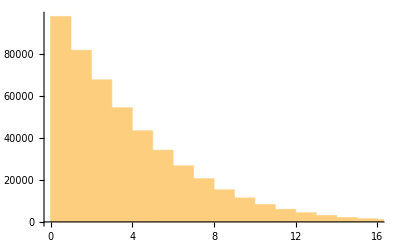

```mathematica
Histogram[allnonzeroes]
```

```mathematica
Max[allnonzeroes]
```

36.6441

```mathematica
Min[allnonzeroes]
```

4.17233×10^-6

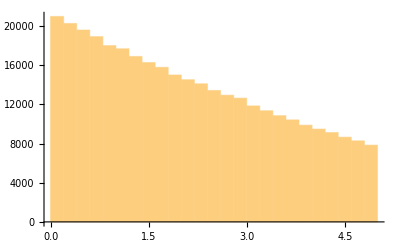

```mathematica
Histogram[Select[allnonzeroes,#<5&]]
```

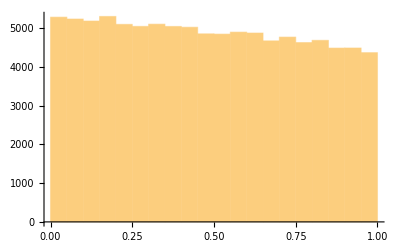

```mathematica
Histogram[Select[allnonzeroes,#<1&]]
```

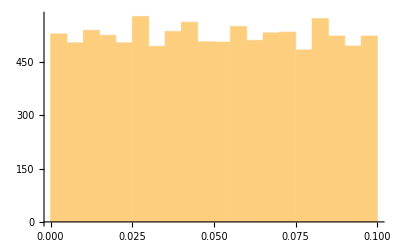

```mathematica
Histogram[Select[allnonzeroes,#<0.1&]]
```

```mathematica
Length[allnonzeroes]
```

481066

```mathematica
thresholds=Table[i,{i,0.0,15.0,0.2}]
```

{0.,0.2,0.4,0.6,0.8,1.,1.2,1.4,1.6,1.8,2.,2.2,2.4,2.6,2.8,3.,3.2,3.4,3.6,3.8,4.,4.2,4.4,4.6,4.8,5.,5.2,5.4,5.6,5.8,6.,6.2,6.4,6.6,6.8,7.,7.2,7.4,7.6,7.8,8.,8.2,8.4,8.6,8.8,9.,9.2,9.4,9.6,9.8,10.,10.2,10.4,10.6,10.8,11.,11.2,11.4,11.6,11.8,12.,12.2,12.4,12.6,12.8,13.,13.2,13.4,13.6,13.8,14.,14.2,14.4,14.6,14.8,15.}

### What if we normalize the vectors?

```mathematica
normalizedVector[r_]:=(
Clear[vect];
vect=vector[r];
Normalize[vect]
)
```

```mathematica
normalizedNonZeros=Flatten[Select[#,(#≠0&)]&/@(normalizedVector/@fullData)];
```

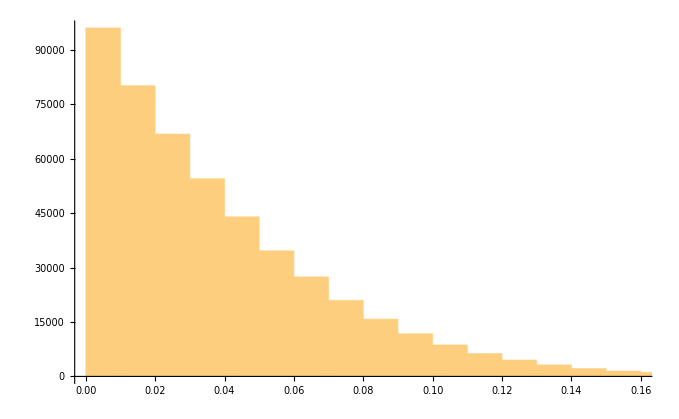

```mathematica
Histogram[normalizedNonZeros]
```

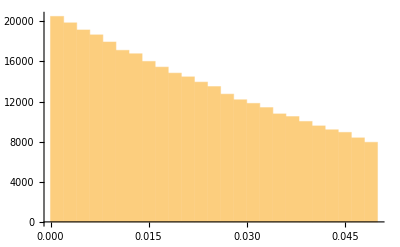

```mathematica
Histogram[Select[normalizedNonZeros,#<0.05&]]
```

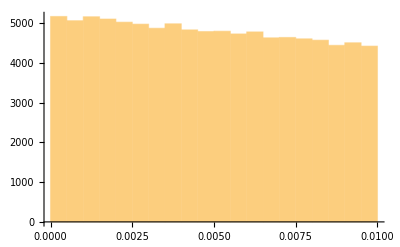

```mathematica
Histogram[Select[normalizedNonZeros,#<0.01&]]
```

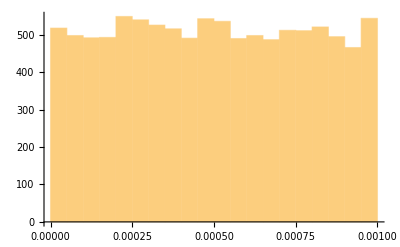

```mathematica
Histogram[Select[normalizedNonZeros,#<0.001&]]
```

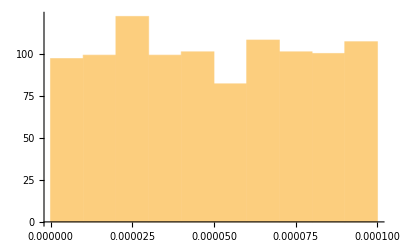

```mathematica
Histogram[Select[normalizedNonZeros,#<0.0001&]]
```

### Analysis of the FB’s

```mathematica
(*Use Import to get the same result as this: fbAnalyzedDataList=allGenuineAndImposterScoresFromDataForSpecificPairs[fullData,"fb",pairsFBList1,#]&/@thresholds;*)
```

```mathematica
(*Export["/Users/ivanevtimov/GDrive-Laf/THESIS/Results with more subjects/mathematica-exports/fbAnalyzedDataList.csv",fbAnalyzedDataList]*)
```

```mathematica
fbAnalyzedDataList=ToExpression[Import["/Users/ivanevtimov/GDrive-Laf/THESIS/Results with more subjects/mathematica-exports/fbAnalyzedDataList.csv","CSV"]];
```

```mathematica
garAt0FarMeasuresFB=garAt0Far/@fbAnalyzedDataList;
```

```mathematica
garVsThreshold=Table[{thresholds[[i]],garAt0FarMeasuresFB[[i]]},{i,1,Length[garAt0FarMeasuresFB]}];
```

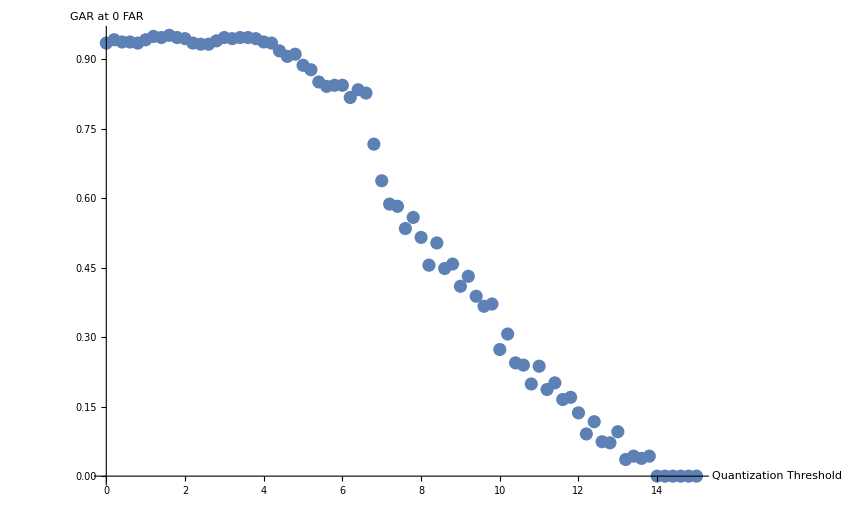

```mathematica
ListPlot[garVsThreshold,AxesLabel->{"Quantization Threshold","GAR at 0 FAR"}]
```

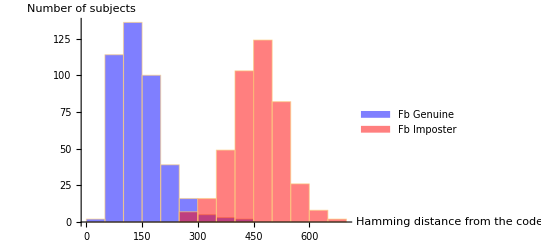

```mathematica
Histogram[{fbAnalyzedDataList[[9]][[All,2]],fbAnalyzedDataList[[9]][[All,4]]},ChartStyle->{Blue,Red},AxesLabel->{"Hamming distance from the code from the fa image", "Number of subjects"},ChartLegends->{"Fb Genuine","Fb Imposter"}]
```

```mathematica
(*TableForm[Table[Histogram[{fbAnalyzedDataList[[i]][[All,2]],fbAnalyzedDataList[[i]][[All,4]]},ChartStyle->{Blue,Red}],{i,1,30}]]*)
```

```mathematica
Table[Count[fbAnalyzedDataList[[i,All,2]],#==0&],{i,Length[fbAnalyzedDataList]}]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
HammingDistance[{0.0000000000000000000000000000001},{0.0000000000000000000000000000002}]
```

1

```mathematica
Norm[Normalize[{1,4,1}]]
```

1

### Analysis of the RC’s

```mathematica
(*Use Import statement: rcAnalyzedDataList=allGenuineAndImposterScoresFromDataForSpecificPairs[fullData,"rc",pairsRCList2,#]&/@thresholds;*)
```

```mathematica
(*Export["/Users/ivanevtimov/GDrive-Laf/THESIS/Results with more subjects/mathematica-exports/rcAnalyzedDataList.csv",rcAnalyzedDataList]*)
```

```mathematica
rcAnalyzedDataList=ToExpression[Import["/Users/ivanevtimov/GDrive-Laf/THESIS/Results with more subjects/mathematica-exports/rcAnalyzedDataList.csv"]];
```

```mathematica
garAt0FarMeasuresRC=garAt0Far/@rcAnalyzedDataList;
```

```mathematica
garVsThresholdRC=Table[{thresholds[[i]],garAt0FarMeasuresRC[[i]]},{i,1,Length[garAt0FarMeasuresRC]}];
```

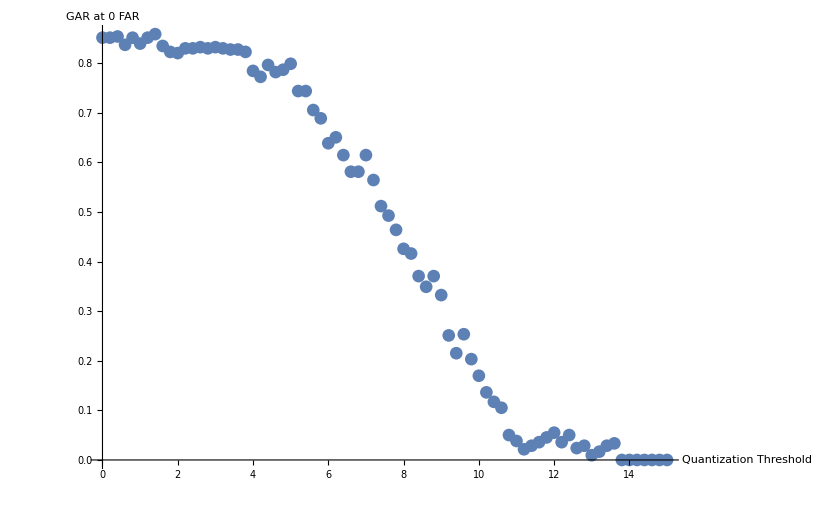

```mathematica
ListPlot[garVsThresholdRC,AxesLabel->{"Quantization Threshold","GAR at 0 FAR"}]
```

```mathematica
Table[Count[rcAnalyzedDataList[[i,All,2]],#==0&],{i,Length[rcAnalyzedDataList]}]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}